### Task number 1

```mathematica
n=126456119090476383371855906671054993650778797793018127;
e=7937;
cipher={60833078379832053733665235104517667174744887177103669,47845135110330425759238983903835414959478333031403660,29226436027122547212719862444995325439654173683124719,26852073219160460393476539289841435348076003235573562,18536789208272843521201394019815486297145984481554371,60946204295190537657611153931568067486237180585452998,23651682987715782801807742133012602969829495021520007,112630050746349041975951827486336529408641182025699787,46387928110260904731968713144311859620686048715174256,101614383351383083936620333816943396668613455381224570};
```

```mathematica
ByteCount[60833078379832053733665235104517667174744887177103669]
BitLength[n]
```

64

177

Get p and q from n

```mathematica
list =FactorInteger[n]
```

{{255471513878248459929909589,1},{494991074232809803525292243,1}}

```mathematica
p = 255471513878248459929909589;
q = 494991074232809803525292243;
```

Calculate phi of n and d

```mathematica
ϕn = (p-1)(q-1)
```

126456119090476383371855905920592405539720534337816296

```mathematica
d =PowerMod[e,-1,ϕn]
```

51350393326018065214500640642820879810321189639760857

```mathematica
B=256;
```

Decrypt the values encoding the message

```mathematica
mFromAlice=PowerMod[cipher,d,n]
```

{2483146643984445192345636330079102759118729027,722369580881590125064109645847105963882455157,2350213338021147253860982007757055631414030196,2329393568285358064614775189816154996921952368,723681021224637848374804982552806414184641633,1117864457951062644410798836349443134030180967,2618954801435453754665981593200392040461443118,2261119653101816489402268744540097089054798706,722462484686687939146265668666610714326038816,716427237904146453947305916305480417970318959}

Convert decoded result to ascii-text

```mathematica
decodedList = {};
For[i=1,i<= Length[mFromAlice],i++,
q=mFromAlice[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
AppendTo[decodedList,FromCharacterCode[ascii]];
]
StringJoin[decodedList]
```

Congratulations! You have now managed to crack the RSA cipher. This means that you have a pass grade for project 2. If you want to pursue a higher grade you need to solve one more problem.

### Task number 2

```mathematica
ClearAll["`*"]
```

Create RSAcrack-function Create a function that  crack RSA-encryption

```mathematica
RSAcrack[cipher_,n_, e_]:=(
list = FactorInteger[n];  (* Calculate p, q, e and d *)
p = list[[1,1]];
q = list[[2,1]];
ϕn = (p-1)(q-1);
d =PowerMod[e,-1,ϕn];
B=256;
decodedMessage=PowerMod[cipher,d,n]; (* Decode the cipher*)
message = {};
For[i=1,i<= Length[decodedMessage],i++, (* Convert decoded values to list of characters *)
q=decodedMessage[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
AppendTo[message,FromCharacterCode[ascii]];
];
StringJoin[message] (* Create a String from list*)
)
```

Encrypt message:  “ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.”

```mathematica
(* Create encryption keys*)
RSAencrypt[messageToEncrypt_,bitSizeN_] := (
pqSize = Floor[bitSizeN/2];
p2 = NextPrime[RandomInteger[{2^pqSize,2^(pqSize+1)}]];
q2 = NextPrime[RandomInteger[{2^pqSize,2^(pqSize+1)}]];
n2 = p2*q2;
ϕn2=(p2-1)*(q2-1);
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[e2=rnd,ϕn2]≠1];
(* Encryption ours message *)
B = 256;
cipherList = {};
(* Split messageToEncrypt into 8 char long chunks, encrypt these and add to list *)
encryptedPackage = {};
For[i = 1, i < StringLength[messageToEncrypt], i=i+8,
splitMessage= StringPart[messageToEncrypt,i;;(i+7);;1];
joinedMessage = StringJoin[splitMessage];
message2=ToCharacterCode[joinedMessage]. B^(Range[StringLength[joinedMessage]]-1);
cipher2=PowerMod[message2,e2,n2];
AppendTo[cipherList,cipher2];
];
AppendTo[encryptedPackage, {n2,e2,cipherList}];
encryptedPackage
)
```

```mathematica
message = "ATTENTION THE UNIVERSE! BY KINGDOMS RIGHT WHEEL.";
cipherList = RSAencrypt[message, 100]
```

{{2235283995318386984503173985423,7065,{421404088186082203247374055699,1666502968089894317452729336209,730589284059838468768909847914,1461973291796185300379352532285,1360721149954591620195884805655,1820219058571806682946581040727}}}

```mathematica
RSAcrack[cipherList,n2,e2]
```

Timing test: Create function that runs X amount of test from BitLength[n] = 100 → 200 and saves the execution-times in list.

```mathematica
timeResult = {};nUsed = {};
For[nSize = 100, nSize < 200, nSize++,
startTime = TimeUsed[];
encryptPackage = RSAencrypt[message,nSize];
n =encryptPackage[[1,1]]; e = encryptPackage[[1,2]]; cipherList = encryptPackage[[1,3]];
RSAcrack[cipherList, n,e];
endTime = TimeUsed[];
totalTime = endTime - startTime;
AppendTo[nUsed, nSize];
AppendTo[timeResult, totalTime]
]
timeResult;
nUsed;
```

```mathematica
data=Transpose[{nUsed,timeResult}]
```

{{100,0.026241},{101,0.050575},{102,0.052188},{103,0.049752},{104,0.049987},{105,0.046389},{106,0.062844},{107,0.063205},{108,0.069135},{109,0.051617},{110,0.059994},{111,0.077583},{112,0.061485},{113,0.067806},{114,0.068282},{115,0.070828},{116,0.076537},{117,0.121021},{118,0.08121},{119,0.101098},{120,0.098134},{121,0.103596},{122,0.138356},{123,0.126164},{124,0.140903},{125,0.150297},{126,0.198584},{127,0.181833},{128,0.21078},{129,0.227942},{130,0.233617},{131,0.229633},{132,0.229929},{133,0.242613},{134,0.319746},{135,0.274122},{136,0.022212},{137,0.28489},{138,0.59978},{139,0.38173},{140,0.447259},{141,0.319331},{142,0.563318},{143,0.463908},{144,0.681003},{145,0.628482},{146,0.836002},{147,0.521718},{148,0.834754},{149,0.807223}}

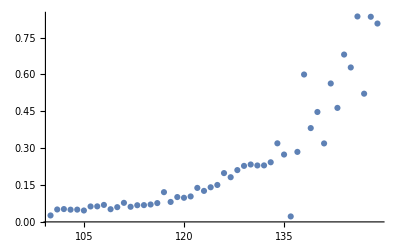

```mathematica
ListPlot[data]
```